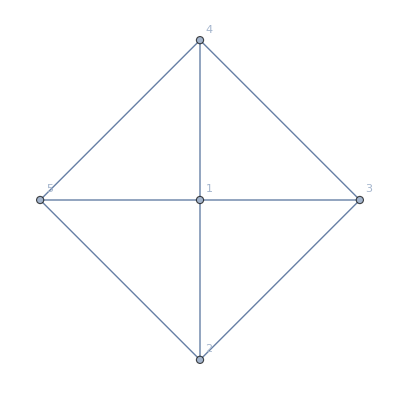

```mathematica
g=WheelGraph[5,VertexLabels->"Name"]
```

```mathematica
gf=Expand[CalculateInOutFormulaMany[g,{{2,3,4,5},{1}}]]
```

14 B1-4 A2 B1+A24 B1-A24x3 B1+A24x35 B1+A24x3x5 B1-A24x5 B1+2 A2x3 B1-A2x35 B1+A2x35x4 B1-A2x3x4 B1+A2x3x4x5 B1-A2x3x5 B1+A2x4 B1-A2x4x5 B1+2 A2x5 B1-4 A3 B1+A35 B1-A35x4 B1+2 A3x4 B1-A3x4x5 B1+A3x5 B1-4 A4 B1+2 A4x5 B1-4 A5 B1

```mathematica
Collect[gf,B1]
```

(14-4 A2+A24-A24x3+A24x35+A24x3x5-A24x5+2 A2x3-A2x35+A2x35x4-A2x3x4+A2x3x4x5-A2x3x5+A2x4-A2x4x5+2 A2x5-4 A3+A35-A35x4+2 A3x4-A3x4x5+A3x5-4 A4+2 A4x5-4 A5) B1

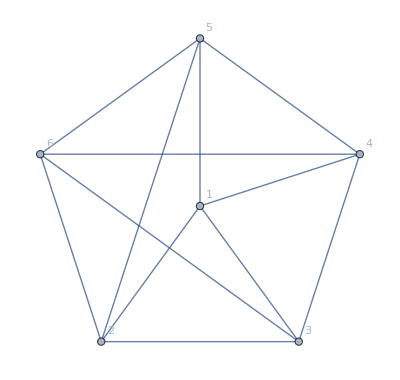

```mathematica
h=EdgeAdd[g,{6<->2,6<->3,6<->4,6<->5}]
```

```mathematica
hf=Expand[CalculateInOutFormulaMany[h,{{2,3,4,5},{1},{6}}]]
```

-64 C6+14 A2 C6-3 A24 C6+A24x3 C6+A24x5 C6-4 A2x3 C6+A2x35 C6+A2x3x4 C6+A2x3x5 C6-3 A2x4 C6+A2x4x5 C6-4 A2x5 C6+14 A3 C6-3 A35 C6+A35x4 C6-4 A3x4 C6+A3x4x5 C6-3 A3x5 C6+14 A4 C6-4 A4x5 C6+14 A5 C6+78 B1 C6-18 A2 B1 C6+4 A24 B1 C6-2 A24x3 B1 C6+A24x35 B1 C6+A24x3x5 B1 C6-2 A24x5 B1 C6+6 A2x3 B1 C6-2 A2x35 B1 C6+A2x35x4 B1 C6-2 A2x3x4 B1 C6+A2x3x4x5 B1 C6-2 A2x3x5 B1 C6+4 A2x4 B1 C6-2 A2x4x5 B1 C6+6 A2x5 B1 C6-18 A3 B1 C6+4 A35 B1 C6-2 A35x4 B1 C6+6 A3x4 B1 C6-2 A3x4x5 B1 C6+4 A3x5 B1 C6-18 A4 B1 C6+6 A4x5 B1 C6-18 A5 B1 C6

```mathematica
hf6=Collect[hf,C6]
```

(-64+14 A2-3 A24+A24x3+A24x5-4 A2x3+A2x35+A2x3x4+A2x3x5-3 A2x4+A2x4x5-4 A2x5+14 A3-3 A35+A35x4-4 A3x4+A3x4x5-3 A3x5+14 A4-4 A4x5+14 A5+78 B1-18 A2 B1+4 A24 B1-2 A24x3 B1+A24x35 B1+A24x3x5 B1-2 A24x5 B1+6 A2x3 B1-2 A2x35 B1+A2x35x4 B1-2 A2x3x4 B1+A2x3x4x5 B1-2 A2x3x5 B1+4 A2x4 B1-2 A2x4x5 B1+6 A2x5 B1-18 A3 B1+4 A35 B1-2 A35x4 B1+6 A3x4 B1-2 A3x4x5 B1+4 A3x5 B1-18 A4 B1+6 A4x5 B1-18 A5 B1) C6

```mathematica
Collect[hf6/C6,B1]
```

-64+14 A2-3 A24+A24x3+A24x5-4 A2x3+A2x35+A2x3x4+A2x3x5-3 A2x4+A2x4x5-4 A2x5+14 A3-3 A35+A35x4-4 A3x4+A3x4x5-3 A3x5+14 A4-4 A4x5+14 A5+(78-18 A2+4 A24-2 A24x3+A24x35+A24x3x5-2 A24x5+6 A2x3-2 A2x35+A2x35x4-2 A2x3x4+A2x3x4x5-2 A2x3x5+4 A2x4-2 A2x4x5+6 A2x5-18 A3+4 A35-2 A35x4+6 A3x4-2 A3x4x5+4 A3x5-18 A4+6 A4x5-18 A5) B1

```mathematica
64/14
```

32/7

```mathematica
14/4
```

7/2

```mathematica
18/14
```

9/7

```mathematica
18/4
```

9/2